# Partial Derivatives and Multivariable Limits

```mathematica
Clear["Global`*"]
```

## Partial Derivatives

Taking partial derivatives is easy in Mathematica... we just use the D function and tell it what variable(s) we want to take derivatives with respect to:

```mathematica
D[Cos[x]+Sin[y],x]
```

```mathematica
D[Cos[x]+Sin[y],x,y]
```

```mathematica
D[Cos[x]+Sin[y],{y,2}]
```

## Limits

Mathematica can take limits, but it can only vary one variable at a time:

```mathematica
f[x_,y_]=(x y +x y^2)/(x^2+y^2);
Limit[f[x,y],x->0]
```

```mathematica
Limit[f[x,y],y->0]
```

Consequently, we must pick a path before using the limit function. Above, we’ve selected paths along the axes, and seen that the resulting limit is zero in both cases. Remember, though, this does not necessarily mean that the limit lim_((x,y)→(0,0)) f(x,y) is equal to zero... let’s look and see what the function looks like:

```mathematica
surface=Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
```

So we see that the limit is likely not zero along the path x=y. To have Mathematica take the limit along this path, we simply plug in x for y:

```mathematica
Limit[f[x,x],x->0]
```

And we see that the limit doesn’t exist because it has a different value along different paths. These paths are plotted below:

```mathematica
path1=ParametricPlot3D[{t,0,f[t,0]},{t,-1,1},PlotStyle->{Thick,Red}];
path2=ParametricPlot3D[{t,t,f[t,t]},{t,-1,1},PlotStyle->{Thick,Green}];
```

```mathematica
Show[{surface,path1,path2}]
```

## Level Curves

As you’ve learned in lecture, the level curves of a function f(x,y) are the curves defined by f(x,y)=c where c is some constant. We can think of this as taking slices of the surface defined by z=f(x,y) which are parallel to the xy plane because we are asking “What does f(x,y) look like at the height c?”

Mathematica’s ContourPlot function makes many of these curves by taking various constants, c, which are equally spaced apart:

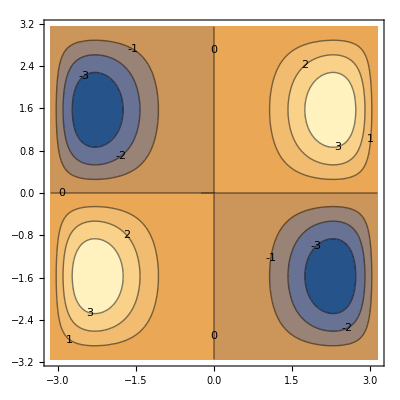

```mathematica
ContourPlot[x^2 Sin[x]Sin[y],{x,-π,π},{y,-π,π},ContourLabels->True]
```

```mathematica
Plot3D[x^2 Sin[x]Sin[y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

We see that the contours appear closer together on steeper parts of the surface. This is a direct result of the fact that we are looking at equally spaced contours. Do you see why?